# 视超光速

视超光速现象指在某些活动星系核的喷流中，观测到的横向运动速度超过光速。这并非违背狭义相对论，而是由于喷流物质以接近光速运动且方向与视线方向夹角极小时，其辐射因多普勒效应和光行时效应导致的几何投影效应，表现为表观超光速运动。

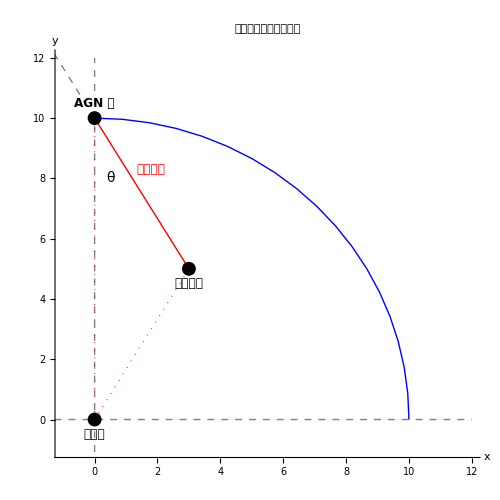

```mathematica
(*视超光速现象几何示意图*)
obs={0,0};           (*观测者*)
core={0,10};         (*AGN 核*)
jetEnd={3,5};        (*喷流指向点*)

(*圆弧参数：半径10，从 y 轴到喷流方向*)
arcRadius=10;
arcStartAngle=90*Pi/180;          (*沿 y 轴方向*)
arcEndAngle=0;

(*绘制图形*)
Graphics[{(*坐标轴*){Gray,Dashed,Line[{{-12,0},{12,0}}],Line[{{0,-2},{0,12}}]},
(*观测者到核的视线*){Red,Dotted,Line[{obs,core}]},
(*观测者到喷流末尾的视线*){Red,Dotted,Line[{obs,jetEnd}]},
(*喷流路径*){Thick,Red,Arrow[{core,jetEnd}]},
(*喷流方向的反向延长线（虚线）*){Gray,Dashed,Line[{core,core+2*(core-jetEnd)}]},
(*以观测者为圆心的圆弧*){Thick,Blue,Circle[obs,arcRadius,{arcStartAngle,arcEndAngle}]},
(*标记夹角 θ*){Black,Text[Style["θ",14,Italic],{0.5,8}]},
(*标注点*){PointSize[0.02],Point[obs],Point[core],Point[jetEnd]},
(*文字标注*)Text[Style["观测者",12],obs+{0,-0.5}],Text[Style["AGN 核",12,Bold],core+{0,0.5}],
Text[Style["喷流末尾",12,Bold],jetEnd+{0,-0.5}],Text[Style["喷流方向",12,Red],jetEnd+{-1.2,3.3}]},
Axes->True,AxesLabel->{"x","y"},
PlotRange->{{-1,12},{-1,12}},ImageSize->500,
AspectRatio->1,
PlotLabel->Style["视超光速现象几何模型",14,Bold]]
```

由上图可见如果喷流和视线方向 （y轴） 存在一个不为90度的夹角，相当于不完全是角向运动，还有视向运动，喷流出发处和一段时间后的喷流末尾与观测者的距离会改变（小角近似情况下距离差为），假设喷流速度为v，夹角为，从核心出发喷流运动时间到达喷流末尾处，那么对于观测者（信息传播速度是光速，接收时间依赖距离），在看见核心处的信号，在接收到在喷流末尾处的信号。

在观测者理解为物体只有角向运动的情况下，观测者以为物体在时间内运动了，那么速度为

```mathematica
vapp[θ_] := v Sin[θ] / (1 - v Cos[θ] / c); (*定义观测者系看到的速度*)
derivative = D[vapp[θ], θ]
```

(v Cos[θ])/(1-(v Cos[θ])/c)-(v^2 Sin[θ]^2)/(c (1-(v Cos[θ])/c)^2)

```mathematica
derivative = Simplify[derivative]
```

(c v (-v+c Cos[θ]))/(c-v Cos[θ])^2

```mathematica
Solve[derivative == 0, Cos[θ]]
```

{{Cos[θ]→v/c}}

由于  Cosθ  在 (0，π/2) 区间内是由大变小，所以导数由正变负，在原函数上即为出现最大值。

```mathematica
(*如果某一喷流运动方向与视向方向夹角θ满足 Cosθ = v/c*)
vappMax=vapp[θ]/. Cos[θ]->v/c/. Sin[θ]->Sqrt[1-(v/c)^2]//Simplify
```

v/(√(1-v^2/c^2))

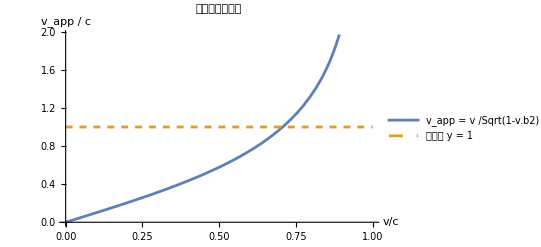

```mathematica
(*设 c=1*)
Plot[{v/Sqrt[1-v^2],1},{v,0,1},AxesLabel->{"v/c","v_app / c"},PlotStyle->{Thick,Dashed},PlotLegends->{"v_app = v /Sqrt(1-v.b2)","水平线 y = 1"},PlotLabel->"表观速度最大值"]
```

```mathematica
Solve[v/Sqrt[1-v^2/c^2] == c, v]
```

{{v→c/(√2)}}

所以只要速度超过0 .707 c，就可以在特定角度下出现视超光速现象。

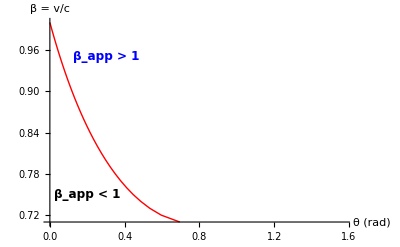

```mathematica
(*视超光速临界曲线：β_app=1 时的 θ 与喷流真实速度 β 的关系*)(*公式：β_app=β sinθ/(1-β cosθ)*)(*设 β_app=1 => β sinθ=1-β cosθ => β (sinθ+cosθ)=1*)

(*解析求解临界角（锐角分支）*)criticalAngle[β_]:=Module[{θ},θ=ArcSin[1/(β Sqrt[2])]-π/4;(*由 sinθ+cosθ=√2 sin(θ+π/4)=1/β*)If[β<1/Sqrt[2],Undefined,θ]]   (*只有 β≥1/√2 时存在解*)

(*生成一系列 β 值及其对应的临界角*)
βList=Range[0.71,1.0,0.01];
θList=criticalAngle/@βList;
points=Transpose[{θList,βList}];

(*绘图：临界曲线将平面分为 β_app>1 (上侧) 和 β_app<1 (下侧)*)
plotCritical=ListLinePlot[points,PlotStyle->{Thick,Red},AxesLabel->{"θ (rad)","β = v/c"},PlotRange->{{0,π/2},{0.71,1}},Epilog->{Text[Style["β_app > 1",12,Bold,Blue],{0.3,0.95}],Text[Style["β_app < 1",12,Bold,Black],{0.2,0.75}]}]
```

红线的右侧都是满足视超光速的，左侧不会发生以及速度小于0 .707 c都不会发生视超光速。